Carbapenem Resistance

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

#### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="United States"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years];
nop = (Length[data]-4)/2;
isolates = data[[2;;Length[data]-3;;2]];
resistance = data[[3;;Length[data]-3;;2]];
rfreq =resistance/isolates;
carbcons = data[[-3]]/40;
conbreak = data[[-2,1;;nop]];
cardiv =Table[carbcons*conbreak[[i]],{i,1,nop}];
pc =  data[[-1,1]]; (*proportion of carbapanem prescription out of all antibiotics prescribed for bacterial pneuomonia NOTE: Update with better estimate.*)
tc = cardiv/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
prop = cardiv/tc;
diff = tc-cardiv;
```

```mathematica
cardiv
```

#### Model

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use. 
The functional form of the model is e^m/(1/Subscript[r, 0] - 1 + e^m)LinguisticAssistant

```mathematica
r[t_,r0_,a_,b_] := ⅇ^(Total[b*cn[[1;;t]]]+b*(a-1)*t)/((1/r0)-1+ⅇ^( Total[b*cn[[1;;t]]]+b*(a-1)*t)) ; (*dA/dt= Subscript[R, C] CA + Subscript[R, N] A, dB/dt= Subscript[N, C] CB + Subscript[N, N] B=> m = a ∑_(i=1)^t Subscript[p, t] Subscript[C, t] + bt and  a = Subscript[R, C]-Subscript[N, C], b=Subscript[R, N]-Subscript[N, N]*)
```

Note: The likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKResistance, above) vs. non-resistant (UKIsolates – UKResistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.

```mathematica
Lik[r0_,a_,b_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,a,b]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,a,b]],{j,1,tt}]]
```

#### Model Fitting

Using NMaximize function to optimize the likelihood function defined above.

```mathematica
max  = PadRight[{},nop,Null];
fr0 = max; fa=max; fb = max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardiv[[i]],df =diff[[i]],{max[[i]],{fr0[[i]],fa[[i]],fb[[i]]}}=NMaximize[{Lik[r0,a,b],0< r0< 1, 0<a<0.8,b>0},{r0,a,b}, MaxIterations->100000]}]
max
mfr0 = Table[fr0[[i]][[2]],{i,1,3}] 
mfa = Table[fa[[i]][[2]],{i,1,3}]
mfb = Table[fb[[i]][[2]],{i,1,3}]
```

{-194.31,-84.7649,-331.512}

{0.00394966,0.166397,0.306284}

{0.8,0.8,0.8}

{1.83069,0.0595707,2.57049}

#### Plots

Putting together observed and fitted data together for plotting.

```mathematica
t=Range[1,tt]; 
res = Table[Transpose@{years,rfreq[[i]]},{i,1,nop}]; (*resistance frequency data*)
x  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardiv[[i]],df =diff[[i]],x[[i]] = Table[r[j,mfr0[[i]],mfa[[i]],mfb[[i]]],{j,1,tt}]}];
fit =  Table[Transpose@{years,x[[i]]},{i,1,nop}];
```

Show plots

```mathematica
plotD = Table[ListPlot[{res[[i]]},PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,PlotLegends->{"Resitance frequency"}],{i,1,nop}];
plotM = Table[ListLinePlot[{fit[[i]]},PlotStyle->{{Orange,Thick}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Model fit"}],{i,1,nop}];
```

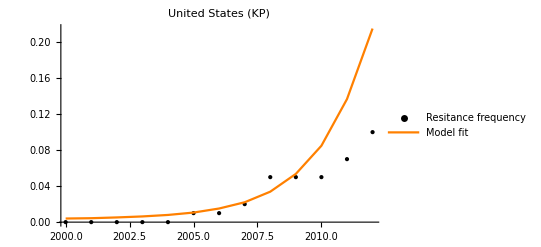

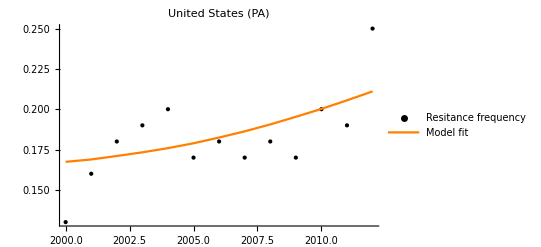

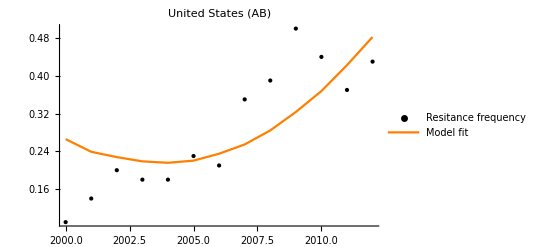

```mathematica
Show[plotD[[1]],plotM[[1]],PlotRange->All,PlotLabel->"United States (KP)"] 
Show[plotD[[2]],plotM[[2]],PlotRange->All,PlotLabel->"United States (PA)"]
Show[plotD[[3]],plotM[[3]],PlotRange->All,PlotLabel->"United States (AB)"]
```

#### Projections

We project the impact of reduction in carbapenem consumption on the antibiotic resistance frequencies in pathogens considered.

```mathematica
curcarb = carbcons[[-1]];  (*current carbapenem consumption*)
py =2030; (*projection till year py*) 
npy = py -years[[-1]];
pyears = Range[ years[[-1]],py];

(*Status Quo consumtions*)
projSQ =ConstantArray[curcarb,Round[npy]];  (*maintaining current carbapenem consumption levels*) 
carbconSQ = Join[carbcons,projSQ];
cardivSQ =Table[carbconSQ*conbreak[[i]],{i,1,nop}];
tcSQ = cardivSQ/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
diffSQ = tcSQ-cardivSQ;
(*Intervention consumtions*)
intv = 0.4; (*reducing current carbapenem consumption by (1-intv) % in next npy years linearly*)

(*For sparing (0 immediately), set approach = 0; for sparing (0 after npy years), set approach = 1; for stewardship (immediate reduction based on intv), set approach = 2; for stewardship (linear reduction to the level described by intv), set approach = 3*)

approach = 2
If[approach==0, projI = ConstantArray[0,Round[npy]], If[approach==1,projI = Range[curcarb,0,(-1)*curcarb/(npy-1)], If[approach==2, projI=ConstantArray[intv*curcarb,Round[npy]], If[approach == 3, projI = Range[curcarb,intv*curcarb,curcarb*(intv-1)/(npy-1)]]]]]
projI
(*projI = Range[curcarb,intv*curcarb,curcarb*(intv-1)/(npy-1)];*)
carbconI = Join[carbcons, projI];
cardivI =Table[carbconI*conbreak[[i]],{i,1,nop}];
tcI = cardivSQ/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
diffI = tcI-cardivI;
(*Status Quo resistances*)
y  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardivSQ[[i]],df =diffSQ[[i]],y[[i]] = Table[r[j,mfr0[[i]],mfa[[a]],mfb[[i]]],{j,tt,tt+npy}]}];
prrSQ =  Table[Transpose@{pyears,y[[i]]},{i,1,nop}];
(*Intervention resistances*)
z  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardivI[[i]],df =diffI[[i]],z[[i]] = Table[r[j,mfr0[[i]],mfa[[i]],mfb[[i]]],{j,tt,tt+npy}]}];
prrI =  Table[Transpose@{pyears,z[[i]]},{i,1,nop}];
```

2

{0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67}

{0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67,0.67}

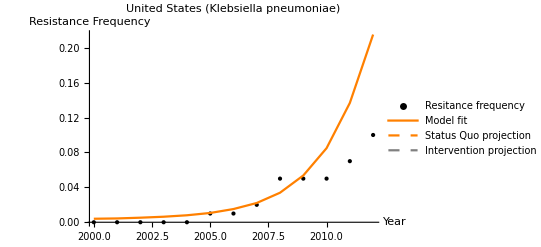

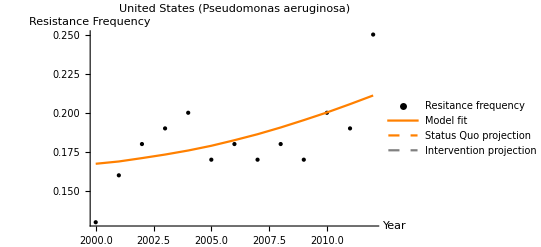

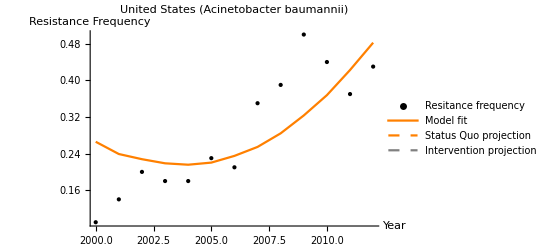

```mathematica
plotPSQ = Table[ListLinePlot[{prrSQ[[i]]},PlotStyle->{{Orange,Thick,Dashed}},PlotStyle->Gray,AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Status Quo projection"}],{i,1,nop}];
plotPI = Table[ListLinePlot[{prrI[[i]]},PlotStyle->{{Gray,Thick,Dashed}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Intervention projection"}],{i,1,nop}];
Show[plotD[[1]],plotM[[1]],plotPSQ[[1]],plotPI[[1]],PlotRange->All,PlotLabel->"United States (Klebsiella pneumoniae)",AxesLabel->{"Year","Resistance Frequency"}] 
Show[plotD[[2]],plotM[[2]],plotPSQ[[2]],plotPI[[2]],PlotRange->All,PlotLabel->"United States (Pseudomonas aeruginosa)",AxesLabel->{"Year","Resistance Frequency"}]
Show[plotD[[3]],plotM[[3]],plotPSQ[[3]],plotPI[[3]],PlotRange->All,PlotLabel->"United States (Acinetobacter baumannii)",AxesLabel->{"Year","Resistance Frequency"}]
```

# Economic & Health Outcomes

```mathematica
(*guhkpcount=351;
guhcrecount=599;
guhcrudeincidence=2.93/100000;
guhpneumonia=0.029;
USpop2013= 316500000;

kprescount=(guhkpcount/guhcrecount)*(guhcrudeincidence)*(guhpneumonia) * (USpop2013);
kppatientcount=kprescount/rbasecase[[1,2]];*)
```

```mathematica
anevlaviscapinc=5610000; (*community acquired pneumonia infections only*)
patientnum=conbreak*anevlaviscapinc;
```

```mathematica
(*carbapenem prescription breakdown for KPC*)
leekp={20/105,19/105,29/105,35/105}; (*carbapenem mono, carbapenem combo, sparing mono, sparing combo*)

(*associated mortality rates*)
rkpmortality={0.467,0.278,0.467,0.304};

(*susceptible mortality rates dummy variables*)
skpmortality={0.234,0.234,0.234,0.234};

(*kp # of deaths*)
kpdeath[r_]:=(Total[leekp*rkpmortality]*r + Total[leekp*skpmortality]*(1-r))*patientnum[[1]];
Apply[kpdeath,{rbasecase[[1]]}]
```

```mathematica
(*Length of stay*)
losinapp=5;
losapp=2;
genwardcost=2877;

(*los is for hospital acquired infections while patient num is for community acquired*)

kploscost[r_]:=0.1*patientnum[[1]]*genwardcost*((losinapp*((r*(leekp[[1]]+leekp[[2]]))+(1-r)*(leekp[[3]]+leekp[[4]])))+(losapp*(r*(leekp[[3]]*leekp[[4]])+((1-r)*(leekp[[1]]+leekp[[2]])))))
Apply[kploscost,{rbasecase[[1]]}] (*multiplied by 10% under assumption that 10% of community acquired pneumonia patients go to hospital*)
```